```mathematica
(* Begin a new round of tests for the Generalized Multinomial Theorem *)
```

```mathematica
(* DEFINITIONS: (from other project) *)
(*Generalized Binomial Coefficients -- y,x in R\Z_(<=-1) . I.e. for fixed y, we can think of genBinom as a function from R\Z_(<=-1) --> R *)
genBinom[y_,x_]:=Module[{y0=y,x0=x},Gamma[1+y0]/(Gamma[1+x0]*Gamma[1+y0-x0])]
(* Generalized Multinomial Coefficients -- n,n_1,...,n_k in R\Z_(<=-1). I.e. for fixed n, we can think of it as a function from (R\Z_(<=-1))^k --> R.  *)
genMultinom[n_,ni__]:=Module[{n0=n, args= ni},
(Gamma[n+1])/(Product[Gamma[i+1],{i,args}])
]
```

```mathematica
(* ================================================================================================================ *)
```

278.378

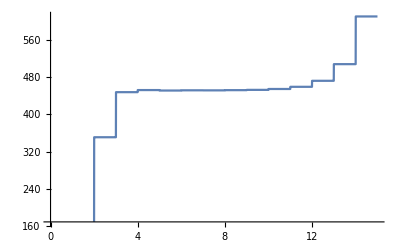

452.096

```mathematica
(* Magnitudes the same; no maximum *)
r = Pi;
xvec = {2,2,2};

N[(Total[xvec])^r]
Plot[N[Sum[Sum[genMultinom[r,{n1,n2,r-n1-n2}]*(xvec[[1]])^(n1)*(xvec[[2]])^(n1)*(xvec[[3]])^(r-n1-n2),{n2,0,x}],{n1,0,x}]],{x,0,15}]
N[Sum[Sum[genMultinom[r,{n1,n2,r-n1-n2}]*(xvec[[1]])^(n1)*(xvec[[2]])^(n1)*(xvec[[3]])^(r-n1-n2),{n2,0,6}],{n1,0,6}]]
```

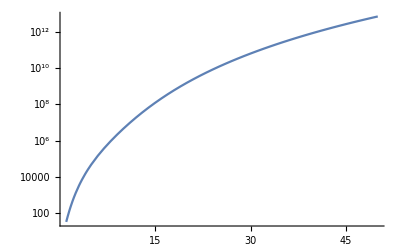

```mathematica
(* I wonder if we can plot the value that the 6th term takes as a function of what's iin the xvec? *)
LogPlot[N[Sum[Sum[genMultinom[r,{n1,n2,r-n1-n2}]*(i)^(n1)*(i)^(n1)*(i)^(r-n1-n2),{n2,0,6}],{n1,0,6}]],{i,1,50}]
```

```mathematica
-2.6629292068145543*^25
(* DIVERGES right away.*)
```

```mathematica
(* Max magnitude i exists, but we give the edecreasing exponent to a different xj. *)
r = Pi;
xvec = {2,-1,I-.1};
x =50;
N[(Total[xvec])^r]
N[Sum[Sum[genMultinom[r,{n1,n2,r-n1-n2}]*(xvec[[1]])^(r-n1-n2)*(xvec[[2]])^(n2)*(xvec[[3]])^(n1),{n2,0,x}],{n1,0,x}]]
```

-2.21764+1.23754 ⅈ

-2.21764+1.23754 ⅈ

```mathematica
(* ALL RIGHT, I WROTE DOWN THE CONJECTURE!!! TIME TO DO SOMETHING ELSE! *)
```